## Floating Point Precision

Double-precision (64-bit) floating point values have 53 bits for representation of the significand. (https://en.wikipedia.org/wiki/Double-precision_floating-point_format)

```mathematica
2^(-53)//N
```

1.11022×10^-16

So lets assume we’re going to need to have 16-17 decimal places of precision in our final formula for calculating .

## Chebyshev Polynomials

Look at the first few Chebyshev polynomials (of the first kind):

```mathematica
Table[{Subscript[T, i],TraditionalForm[ChebyshevT[i,x]]},{i,0,12}]//TableForm
```

T_0 | 1
T_1 | x
T_2 | 2 x^2-1
T_3 | 4 x^3-3 x
T_4 | 8 x^4-8 x^2+1
T_5 | 16 x^5-20 x^3+5 x
T_6 | 32 x^6-48 x^4+18 x^2-1
T_7 | 64 x^7-112 x^5+56 x^3-7 x
T_8 | 128 x^8-256 x^6+160 x^4-32 x^2+1
T_9 | 256 x^9-576 x^7+432 x^5-120 x^3+9 x
T_10 | 512 x^10-1280 x^8+1120 x^6-400 x^4+50 x^2-1
T_11 | 1024 x^11-2816 x^9+2816 x^7-1232 x^5+220 x^3-11 x
T_12 | 2048 x^12-6144 x^10+6912 x^8-3584 x^6+840 x^4-72 x^2+1

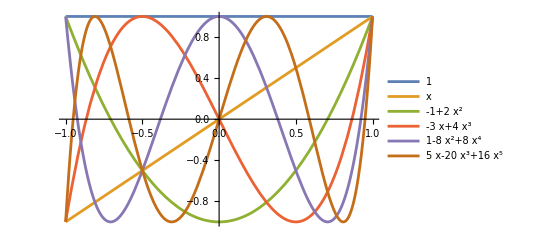

```mathematica
Plot[Evaluate[Table[ChebyshevT[i,x],{i,0,5}]],{x,-1,1},
PlotLegends->"Expressions"]
```

Chebyshev  polynomials  are  orthogonal  with  the  following  product :

```mathematica
innerProd[f_,g_]:=2/π∫_-1^1 (f[x]g[x])/(√(1-x^2))ⅆx
```

```mathematica
innerProd[ChebyshevT[3,#]&,ChebyshevT[3,#]&]
```

1

```mathematica
innerProd[ChebyshevT[1,#]&,ChebyshevT[2,#]&]
```

0

```mathematica
Table[innerProd[ChebyshevT[i,#]&,ChebyshevT[j,#]&],{i,0,5},{j,0,5}]//TableForm
```

2 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1

We can calculate the coefficients of the Chebyshev expansion for a function by projecting the function onto the individual Chebyshev functions.

```mathematica
innerProd[ChebyshevT[3,#]&,Sin[Pi*#/2]&]
```

-2 BesselJ[3,π/2]

```mathematica
coef[n_]:=Integrate[
(2Sin[x*π/2]*ChebyshevT[n,x])/(π √(1-x^2)),
{x,-1,1}]
```

```mathematica
sinCoefficients1=Table[
Evaluate[innerProd[Sin[#*Pi/2]&, ChebyshevT[i,#]&]],
{i,0,20}];
```

```mathematica
sinCoefficients1[[1;;8]]//TableForm
```

0
2 BesselJ[1,π/2]
0
-2 BesselJ[3,π/2]
0
(2 (π (-192+π^2) BesselJ[1,π/2]-24 (-64+π^2) BesselJ[2,π/2]))/π^3
0
(2 (π (92160-960 π^2+π^4) BesselJ[1,π/2]-48 (15360-320 π^2+π^4) BesselJ[2,π/2]))/π^5

```mathematica
N[sinCoefficients1,12]//TableForm
```

0
1.13364817781
0
-0.138071776587
0
0.00449071424655
0
-0.0000677012758422
0
5.89129533029×10^-7
0
-3.33805940892×10^-9
0
1.32970283845×10^-11
0
-3.92749958718×10^-14
0
8.94526011594×10^-17
0
-1.61896899669×10^-19
0

```mathematica
sinApproximation1[i_,digits_:24]:=Simplify[
N[sinCoefficients1[[1;;(i+1)]],digits].Table[ChebyshevT[d,x],{d,0,i}]
]
```

```mathematica
Table[sinApproximation1[i,5],{i,0,12}]//TableForm
```

0
1.1336 x
1.1336 x
1.5479 x-0.55229 x^3
1.5479 x-0.55229 x^3
1.5703 x-0.6421 x^3+0.071851 x^5
1.5703 x-0.6421 x^3+0.071851 x^5
1.5708 x-0.64589 x^3+0.079434 x^5-0.0043329 x^7
1.5708 x-0.64589 x^3+0.079434 x^5-0.0043329 x^7
1.5708 x-0.64596 x^3+0.079688 x^5-0.0046722 x^7+0.00015082 x^9
1.5708 x-0.64596 x^3+0.079688 x^5-0.0046722 x^7+0.00015082 x^9
1.5708 x-0.64596 x^3+0.079693 x^5-0.0046816 x^7+0.00016022 x^9-3.4182×10^-6 x^11
1.5708 x-0.64596 x^3+0.079693 x^5-0.0046816 x^7+0.00016022 x^9-3.4182×10^-6 x^11

Here’s the 10th degree approximation:

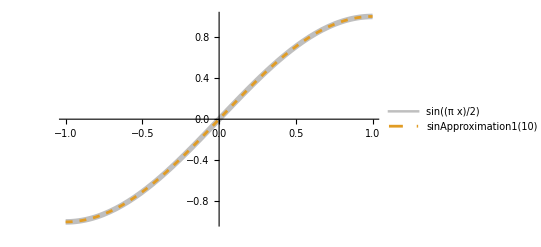

```mathematica
Plot[{Sin[Pi*x/2],sinApproximation1[10]},{x,-1,1},
PlotLegends->"Expressions",
PlotStyle->{{Thickness[0.01],Opacity[0.5],Gray},Dashed}]
```

Even the 3rd degree approximation is pretty good:

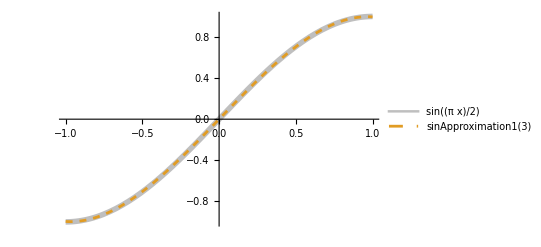

```mathematica
Plot[{Sin[Pi*x/2],sinApproximation1[3]},{x,-1,1},
PlotLegends->"Expressions",
PlotStyle->{{Thickness[0.01],Opacity[0.5],Gray},Dashed}]
```

The error gets small very quickly:

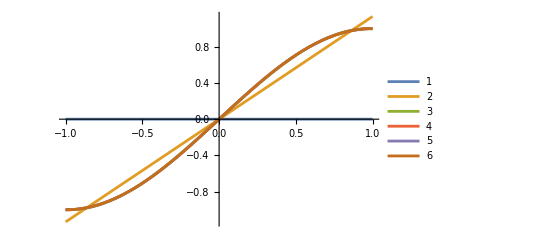

```mathematica
Plot[
Evaluate[Table[sinApproximation1[2*i],{i,0,5}]],
{x,-1,1},PlotLegends->Automatic]
```

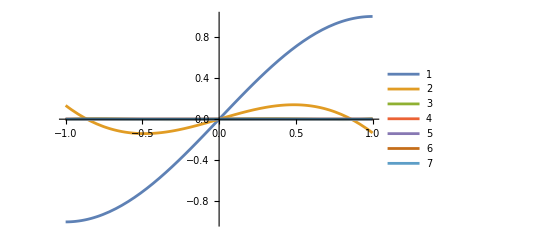

```mathematica
Plot[
Evaluate[Table[Sin[Pi*x/2]-sinApproximation1[2*i],{i,0,6}]],{x,-1,1},
PlotRange->All,PlotLegends->Automatic]
```

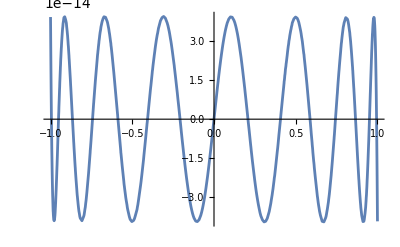

```mathematica
Plot[Sin[Pi*x/2]-sinApproximation1[14],{x,-1,1}]
```

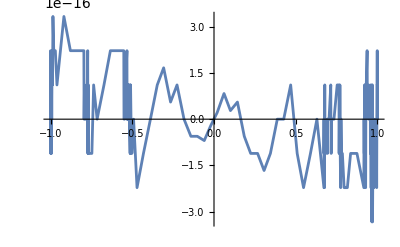

```mathematica
Plot[Sin[Pi*x/2]-sinApproximation1[16],{x,-1,1}]
```

Here we’re getting into the realm of machine precision, so we need to increase Mathematica’s precision in order to get a reasonable plot:

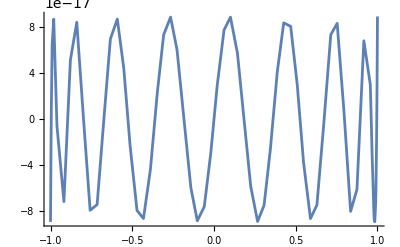

```mathematica
Plot[Sin[Pi*x/2]-sinApproximation1[16],{x,-1,1},WorkingPrecision->30]
```

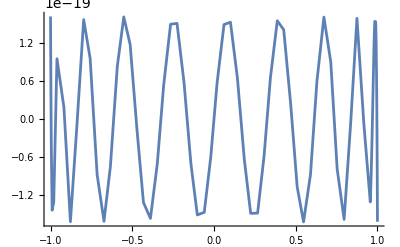

```mathematica
Plot[Sin[Pi*x/2]-sinApproximation1[17],{x,-1,1},WorkingPrecision->30]
```

The approximation of order 17 seems to be good enough for our purposes.

```mathematica
sinApproximation1[17]
```

1.57079632679489661615027 x-0.645964097506246068725494 x^3+0.0796926262461637888741028 x^5-0.00468175413529262296007412 x^7+0.00016044118467432315851806 x^9-3.59884294716944654024508×10^-6 x^11+5.69212853539005432284504×10^-8 x^13-6.68396586459246317556172×10^-10 x^15+5.86236566958322852534316×10^-12 x^17

```mathematica
Chop[CoefficientList[sinApproximation1[17],x],10^-50]
```

{0,1.57079632679489661615027,0,-0.645964097506246068725494,0,0.0796926262461637888741028,0,-0.00468175413529262296007412,0,0.00016044118467432315851806,0,-3.59884294716944654024508×10^-6,0,5.69212853539005432284504×10^-8,0,-6.68396586459246317556172×10^-10,0,5.86236566958322852534316×10^-12}

```mathematica
ExportString[#,"Real64"]&/@CoefficientList[sinApproximation1[17],x]
```

{.00.00.00.00.00.00.00.00,.18-DTû!ù?,.00.00.00.00.00.00.00.00,Q.be%æ.bc«ä¿,.00.00.00.00.00.00.00.00,÷©ug.bcf.b4?,.00.00.00.00.00.00.00.00,#HbÎ,-s¿,.00.00.00.00.00.00.00.00,5E?H.83.07%?,.00.00.00.00.00.00.00.00,.b4.b2^Õt0Î.be,.00.00.00.00.00.00.00.00,Ø¿.04.af3.8fn>,.00.00.00.00.00.00.00.00,.06=.11OG÷.06.be,.00.00.00.00.00.00.00.00,Gv±ÜoÈ.99=}

```mathematica
ToCharacterCode[ExportString[#,"Real64"]&/@CoefficientList[sinApproximation1[17],x]]
```

{{0,0,0,0,0,0,0,0},{24,45,68,84,251,33,249,63},{0,0,0,0,0,0,0,0},{81,190,37,230,188,171,228,191},{0,0,0,0,0,0,0,0},{247,169,117,103,188,102,180,63},{0,0,0,0,0,0,0,0},{35,72,98,206,44,45,115,191},{0,0,0,0,0,0,0,0},{53,69,63,72,131,7,37,63},{0,0,0,0,0,0,0,0},{180,178,94,213,116,48,206,190},{0,0,0,0,0,0,0,0},{216,191,4,175,51,143,110,62},{0,0,0,0,0,0,0,0},{6,61,17,79,71,247,6,190},{0,0,0,0,0,0,0,0},{71,118,177,220,111,200,153,61}}

```mathematica
Map[
IntegerString[#,16,2]&,
ToCharacterCode[ExportString[#,"Real64"]&/@CoefficientList[sinApproximation1[17],x]],
{2}
]
```

{{00,00,00,00,00,00,00,00},{18,2d,44,54,fb,21,f9,3f},{00,00,00,00,00,00,00,00},{51,be,25,e6,bc,ab,e4,bf},{00,00,00,00,00,00,00,00},{f7,a9,75,67,bc,66,b4,3f},{00,00,00,00,00,00,00,00},{23,48,62,ce,2c,2d,73,bf},{00,00,00,00,00,00,00,00},{35,45,3f,48,83,07,25,3f},{00,00,00,00,00,00,00,00},{b4,b2,5e,d5,74,30,ce,be},{00,00,00,00,00,00,00,00},{d8,bf,04,af,33,8f,6e,3e},{00,00,00,00,00,00,00,00},{06,3d,11,4f,47,f7,06,be},{00,00,00,00,00,00,00,00},{47,76,b1,dc,6f,c8,99,3d}}

```mathematica
Map[StringJoin,
Map[
IntegerString[#,16,2]&,
ToCharacterCode[ExportString[#,"Real64"]&/@CoefficientList[sinApproximation1[17],x]],
{2}
]
]
```

{0000000000000000,182d4454fb21f93f,0000000000000000,51be25e6bcabe4bf,0000000000000000,f7a97567bc66b43f,0000000000000000,234862ce2c2d73bf,0000000000000000,35453f488307253f,0000000000000000,b4b25ed57430cebe,0000000000000000,d8bf04af338f6e3e,0000000000000000,063d114f47f706be,0000000000000000,4776b1dc6fc8993d}

```mathematica
IntegerDigits[FromDigits["182d4454fb21f93f",16],2]
```

{1,1,0,0,0,0,0,1,0,1,1,0,1,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,1,1,1,1,1,0,1,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1}

```mathematica
hexRepresentation[x_Real]:=
StringJoin[
Map[IntegerString[#,16,2]&,
ToCharacterCode[
ExportString[x,"Real64"]]]
]
```

```mathematica
hexRepresentation[3.14]
```

1f85eb51b81e0940

```mathematica
binaryDigits[x_Real]:=
IntegerDigits[FromDigits[ResourceFunction["RealToHexString"][x],16],2,64]
```

```mathematica
binaryDigits[3.14]
```

{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,1}

```mathematica
floatFormat[x_Real]:=
Module[{bd=binaryDigits[x]},
{sign->FromDigits[{bd[[1]]},2],exponent->FromDigits[bd[[2;;12]],2]-1023,significand->(FromDigits[bd[[13;;64]],2]+1)/(2^52)}
]
```

```mathematica
floatFormat[3.14]
```

{sign→0,exponent→1,significand→80220368362537/140737488355328}

```mathematica
floatFormat[20000.]
```

{sgn→0,exp→{1,0,0,0,0,0,0,1,1,0,1},mantissa→{0,0,1,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
floatFormat[-3.14]
```

{sgn→1,exp→{1,0,0,0,0,0,0,0,0,0,0},mantissa→{1,0,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,1}}

```mathematica
IntegerDigits[FromDigits[exp/.floatFormat[3.14],2],2]
```

{1,0,0,0,0,0,0,0,0,0,0}

```mathematica
IntegerDigits[FromDigits[[3.14,256],256],2,64]
```

```mathematica
ResourceFunction["RealToHexString"][3.14]
```

40091eb851eb851f

```mathematica
IntegerDigits[FromDigits[ResourceFunction["RealToHexString"][3.14],16],2,64]
```

{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,1}

```mathematica
IntegerDigits[FromDigits[ResourceFunction["RealToHexString"][-3.14],16],2,64]
```

{1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,1}

```mathematica
asFloatString[x_Real]:=
Module[{bd=binaryDigits[x],sgn,exp,mant},
sgn=FromDigits[{bd[[1]]},2];
exp=FromDigits[bd[[2;;12]],2]-1023;
mant=FromDigits[bd[[13;;64]],2];
StringJoin[
If[sgn==0,"+","-"],
"1.",
IntegerString[mant,2,52],
" x 2^",
IntegerString[exp,2,11]
]
]
```

```mathematica
asFloatString[3.14]
```

+1.1001000111101011100001010001111010111000010100011111 x 2^00000000001

```mathematica
asFloat[x_Real]:=
Module[{bd=binaryDigits[x],sgn,exp,mant},
sgn=FromDigits[{bd[[1]]},2];
exp=FromDigits[bd[[2;;12]],2]-1023;
mant=FromDigits[bd[[13;;64]],2];
N[If[sgn==0,+1,-1] * (1 + mant/2^52)*2^exp ]
]
```

```mathematica
asFloat[3.14]
```

3.14

```mathematica
asFloat[0.]
```

General::munfl: 1/(89884656743115795386465259539451236680898848947115328636715040578866337902750481566354238661203768010560056939935696678829394884407208311246423«21»712432742638151109800623047059726541476042502884419075341171231440736956555270413618581675255342293149119973622969239858152417678164812112068608) is too small to represent as a normalized machine number; precision may be lost.

1.11254×10^-308

```mathematica
asFloat[10.]
```

10.

## Normalization

```mathematica
T[0]:=(ChebyshevT[0,#]/Sqrt[Pi])&
T[i_Integer]:=(ChebyshevT[i,#]/Sqrt[Pi/2])&
```

```mathematica
T[0]
```

ChebyshevT[0,#1]/(√π)&

```mathematica
T[0][1.3]
```

0.56419

```mathematica
T[3][x]
```

√(2/π) (-3 x+4 x^3)

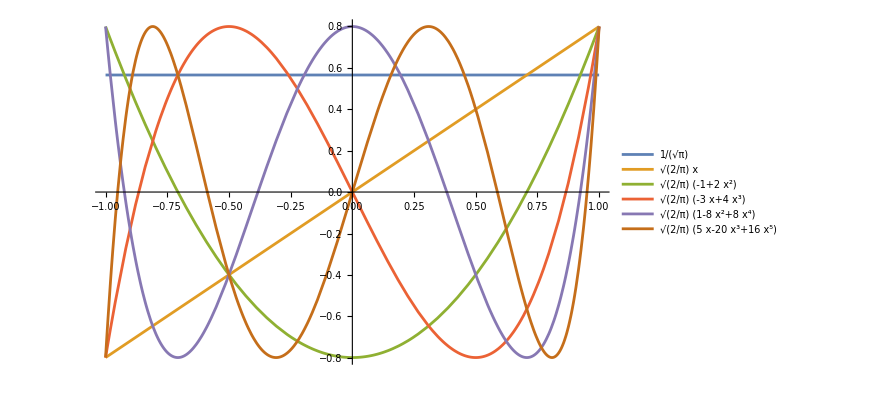

```mathematica
Plot[Evaluate[Table[T[i][x],{i,0,5}]],{x,-1,1},
PlotLegends->"Expressions"]
```

```mathematica
Table[
Integrate[(T[i][x]*T[j][x])/(√(1-x^2)),{x,-1,1}],
{i,0,5},{j,0,5}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1

```mathematica
Table[∫_-1^1 (T[i][x]*T[j][x])/(√(1-x^2))ⅆx,{i,0,5},{j,0,5}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1

```mathematica
innerProduct[f_,g_]:=∫_-1^1 (f[x]*g[x])/(√(1-x^2))ⅆx
```

```mathematica
innerProduct[T[1],T[2]]
```

0

```mathematica
innerProduct[T[1],Sin]
```

√(2 π) BesselJ[1,1]

```mathematica
innerProduct[T[1],Sin]//N
```

1.10304

```mathematica
NIntegrate[(T[3][x]*T[2][x])/(√(1-x^2)),{x,-1,1}]
```

-2.77556×10^-17

```mathematica
innerProductN[f_,g_]:=NIntegrate[(f[x]*g[x])/(√(1-x^2)),{x,-1,1},PrecisionGoal->18,WorkingPrecision->64]
```

```mathematica
Table[{i,innerProductN[T[i],Sin[Pi*#/2]&]},{i,0,24}]//TableForm
```

0 | 0.
1 | 1.420817287993419621827686337373105253782599598266574841398544928
2 | 0.
3 | -0.1730473095609951566947439729462274136537614719927265263274713817
4 | 0.
5 | 0.005628275651851403639709376069781329291720182568389713314075499712
6 | 0.
7 | -0.00008485096612726606722101890597684328358510891098587284634777582229
8 | 0.
9 | 7.383643724552385859762704298651691376995297931043241810608200487×10^-7
10 | 0.
11 | -4.183637048396731819784010067708663102793394481473521979964893126×10^-9
12 | 0.
13 | 1.66653536585664331649799415860342279596997916301641007261755561×10^-11
14 | 0.
15 | -4.922390756913075022148307035241838965937888555909584092587359933×10^-14
16 | 0.
17 | 1.121122096527360389761386748818794703717027047752161616042104844×10^-16
18 | 0.
19 | -2.029076731429751254120007590347292864207052540166977508342749368×10^-19
20 | 0.
21 | 2.988471144759487574684163777133537678400087878412817285399409357×10^-22
22 | 0.
23 | -3.651697160026653256973265579881123157208500529026115011922209887×10^-25
24 | 0.

```mathematica
sinCoefficients=Chop[
Table[innerProductN[T[i],Sin[Pi*#/2]&],{i,0,24}],
10^-50]
```

{0,1.420817287993419621827686337373105253782599598266574841398544928,0,-0.1730473095609951566947439729462274136537614719927265263274713817,0,0.005628275651851403639709376069781329291720182568389713314075499712,0,-0.00008485096612726606722101890597684328358510891098587284634777582229,0,7.383643724552385859762704298651691376995297931043241810608200487×10^-7,0,-4.183637048396731819784010067708663102793394481473521979964893126×10^-9,0,1.66653536585664331649799415860342279596997916301641007261755561×10^-11,0,-4.922390756913075022148307035241838965937888555909584092587359933×10^-14,0,1.121122096527360389761386748818794703717027047752161616042104844×10^-16,0,-2.029076731429751254120007590347292864207052540166977508342749368×10^-19,0,2.988471144759487574684163777133537678400087878412817285399409357×10^-22,0,-3.651697160026653256973265579881123157208500529026115011922209887×10^-25,0}

```mathematica
sinApproximation[i_]:=sinCoefficients[[1;;i+1]].Evaluate[Table[T[j][x],{j,0,i}]]//Simplify
```

```mathematica
sinApproximation[1]
```

1.133648177811747875422489926934320567080634831082979977879687178 x

```mathematica
sinApproximation[6]
```

1.57031707880609877559460779366687186951416003537733929255883751 x-0.642101391279866772398366796153653005148670199298768406224455792 x^3+0.0718514279448786866026515686123015222847639122875471839827064203 x^5

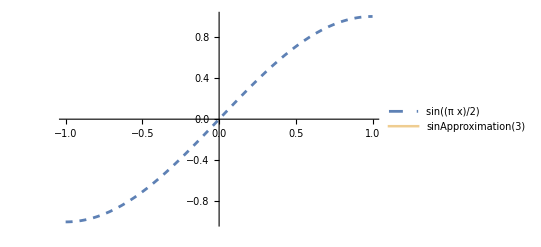

```mathematica
Plot[{Sin[Pi*x/2],sinApproximation[3]},{x,-1,1},PlotLegends->"Expressions",PlotStyle->{Dashed,{Thickness[0.01],Opacity[0.5]}}]
```

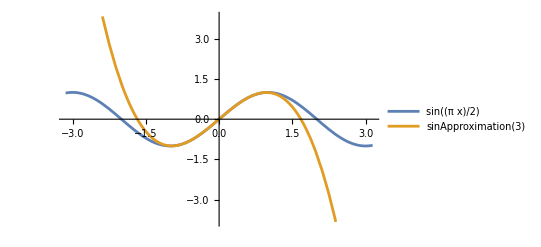

```mathematica
Plot[{Sin[Pi*x/2],sinApproximation[3]},{x,-Pi,Pi},PlotLegends->"Expressions"]
```

```mathematica
$MachinePrecision
```

15.9546

## Orthogonality

```mathematica
chebProduct[f_,g_]:=∫_-1^1 (f[x]*g[x])/(√(1-x^2))ⅆx
```

```mathematica
chebProduct[(1 &), # &]
```

0

```mathematica
projection[f_,g_]:=chebProduct[f,g]/chebProduct[g,g] g
```

```mathematica
projection[(#^2 &),1 &]
```

(1&)/2

```mathematica
projection[#^3&,#&]
```

(3 (#1&))/4

```mathematica
Projection[(#^2 &),1 &,chebProduct]
```

(1&)/2

```mathematica
Orthogonalize[{1,x,x^2,x^3,x^4},{f,g}|->∫_-1^1 (f*g)/(√(1-x^2))ⅆx]
```

{1/(√π),√(2/π) x,2 √(2/π) (-1/2+x^2),4 √(2/π) (-(3 x)/4+x^3),8 √(2/π) (1/8-x^2+x^4)}

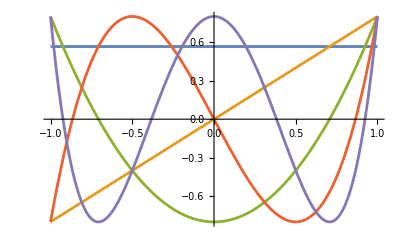

```mathematica
Plot[%,{x,-1,1}]
```

## Nodes

### Calculating Chebyshev Nodes

```mathematica
chebNodes[n_Integer,bounds_List:{-1,1}]:=Table[
(bounds[[1]]+bounds[[2]])/2+(bounds[[2]]-bounds[[1]])/2 Cos[(2*k+1)/(2*n)π],{k,0,n-1}]
```

```mathematica
chebNodes[6]//N
```

{0.965926,0.707107,0.258819,-0.258819,-0.707107,-0.965926}

```mathematica
chebNodes[6,{0,Pi/2}]//N
```

{1.54403,1.34076,0.988674,0.582122,0.230038,0.0267618}

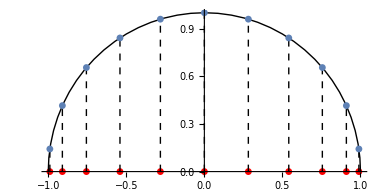

```mathematica
n=11;
Show[
ListPlot[N[Transpose[{chebNodes[n],Table[0,n]}]],PlotStyle->{Large,Red},AspectRatio->1],
Graphics[Circle[{0,0},1,{0,Pi}]],
Graphics[{Dashed,Table[Line[{{Cos[(2*k+1)/(2*n)π],0},{Cos[(2*k+1)/(2*n)π],Sin[(2*k+1)/(2*n)π]}}],{k,0,n-1}]}],
ListPolarPlot[
Table[{(2*k+1)/(2*n)π,1},{k,0,n-1}]],
PlotRange->{{-1.0,1.0},{-0,1.0}},
AspectRatio->1/2
]
```

### Approximation Using Nodes

To approximate a function over an interval  using Chebyshev polynomials up to degree ,

First, compute the Chebyshev nodes on the interval :

for

Then evaluate the function  at the nodes:

for

Define the translated Chebyshev functions on  as:

Set up the matrix of Chebyshev polynomials evaluated at the nodes:

In other words, each row consists of one of the Chebyshev polynomials from  to  evaluated at each of the nodes from , like this:

```mathematica
Table[,{i,0,5},{k,1,6}]//TraditionalForm
```

(T_0(r_1) | T_0(r_2) | T_0(r_3) | T_0(r_4) | T_0(r_5) | T_0(r_6)
T_1(r_1) | T_1(r_2) | T_1(r_3) | T_1(r_4) | T_1(r_5) | T_1(r_6)
T_2(r_1) | T_2(r_2) | T_2(r_3) | T_2(r_4) | T_2(r_5) | T_2(r_6)
T_3(r_1) | T_3(r_2) | T_3(r_3) | T_3(r_4) | T_3(r_5) | T_3(r_6)
T_4(r_1) | T_4(r_2) | T_4(r_3) | T_4(r_4) | T_4(r_5) | T_4(r_6)
T_5(r_1) | T_5(r_2) | T_5(r_3) | T_5(r_4) | T_5(r_5) | T_5(r_6))

```mathematica
translatedCheby[n_,x_,bounds_:{-1,1}]:=ChebyshevT[n,2(x-bounds[[1]])/(bounds[[2]]-bounds[[1]])-1]
```

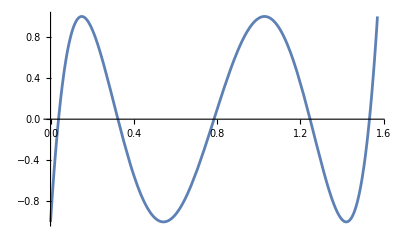

```mathematica
Plot[translatedCheby[5,x,{0,Pi/2}],{x,0,Pi/2}]
```

```mathematica
nodeMatrix[n_,bounds_:{-1,1}]:=Table[translatedCheby[i,chebNodes[n+1,bounds][[j]],bounds],{i,0,n},{j,1,n+1}]
```

```mathematica
nodeMatrix[5,{-1,1}]//N//MatrixForm
```

(1. | 1. | 1. | 1. | 1. | 1.
0.965926 | 0.707107 | 0.258819 | -0.258819 | -0.707107 | -0.965926
0.866025 | 0. | -0.866025 | -0.866025 | 0. | 0.866025
0.707107 | -0.707107 | -0.707107 | 0.707107 | 0.707107 | -0.707107
0.5 | -1. | 0.5 | 0.5 | -1. | 0.5
0.258819 | -0.707107 | 0.965926 | -0.965926 | 0.707107 | -0.258819)

```mathematica
Diagonal[nodeMatrix[5,{-1,1}].Transpose[nodeMatrix[5,{-1,1}]]]//N
```

{6.,3.,3.,3.,3.,3.}

```mathematica
y=Sin[chebNodes[6,{0,Pi/2}]]//N
```

{0.999642,0.973658,0.835298,0.549798,0.228014,0.0267586}

3.15159609307366933583264330573764×10^-17+0.9999999999999921374639814299916625964302946109236 x+3.24848403977218879514297839701634301×10^-13 x^2-0.1666666666719456464058870820368161164261399511809 x^3+4.469299400619199651521470627043949150507×10^-11 x^4+0.00833333310712103651500584264109602941740765926915 x^5+7.39903364746182917886826414295579511841526×10^-10 x^6-0.000198414335571346275936299643363457938137866777378 x^7+2.5124179040125369672342122114110747692542061×10^-9 x^8+2.75303544969185019022074458942258710665139474202×10^-6 x^9+2.006509711219114877007790551706389837889548676×10^-9 x^10-2.60546344930653900663443977065730626732219901854×10^-8 x^11+3.112435370803039020688665795993143330003027774×10^-10 x^12+1.12392760716968552199772568392627738565685544985×10^-10 x^13

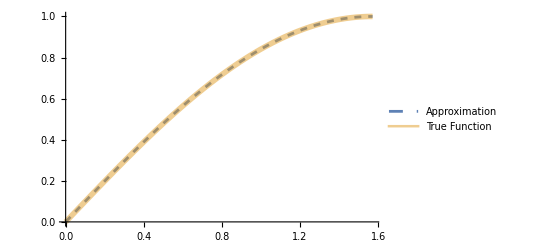

Plot::precw: The precision of the argument function ((3.15159609307366933583264330573764×10^-17+0.9999999999999921374639814299916625964302946109236 x+«8»+2.5124179040125369672342122114110747692542061×10^-9 x^8+2.75303544969185019022074458942258710665139474202×10^-6 x^9+«4»)-f[x]) is less than WorkingPrecision (50.).

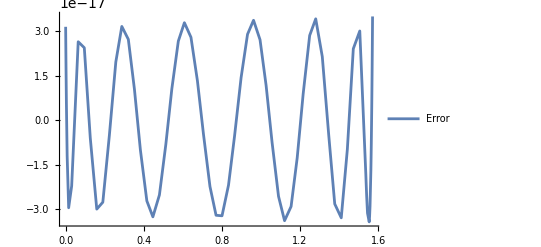

```mathematica
f=Sin;
bounds={0,Pi/2};
degree=13;
precision=50;
m=nodeMatrix[degree,bounds];
y=f[chebNodes[degree+1,bounds]];
coefficients =(m.y)/Diagonal[m.Transpose[m]];
fApprox=N[
coefficients.Table[translatedCheby[i,x,bounds],{i,0,degree}],
precision]//Simplify
Plot[
{fApprox,f[x]},
{x,bounds[[1]],bounds[[2]]},
PlotStyle->{Dashed,{Thickness[0.01],Opacity[0.5]}},
PlotLegends->{"Approximation","True Function"}]
Plot[
fApprox-f[x],
{x,bounds[[1]],bounds[[2]]},
PlotLegends->{"Error"},WorkingPrecision->precision]
```

It looks like a polynomial of degree 13 gives sufficient accuracy for our needs.

## GSL

If the GNU Scientific Library is compiled, we can call its  function from Mathematica:

```mathematica
gslSin=ForeignFunctionLoad["/usr/local/lib/libgsl","gsl_sf_sin",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
gslSin[0.5]
```

0.479426

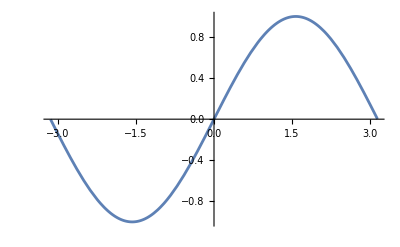

```mathematica
Plot[gslSin[x],{x,-3.14,3.14}]
```

It’s accurate to machine precision, or pretty close.

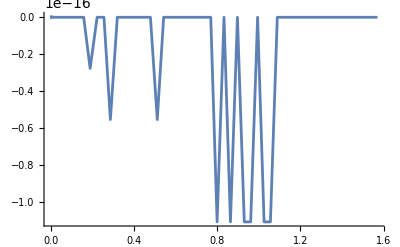

```mathematica
Plot[gslSin[x]-Sin[x],{x,0,Pi/2},WorkingPrecision->24]
```

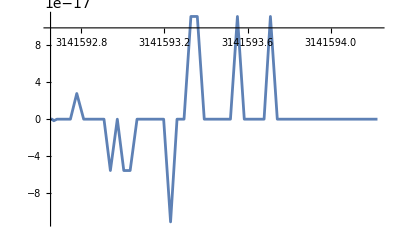

```mathematica
Plot[gslSin[x]-Sin[x],{x,N[π*10^6],N[π*10^6+π/2]},WorkingPrecision->24]
```

## References

https://en.wikipedia.org/wiki/Chebyshev_polynomials
https://www.johndcook.com/blog/2020/03/11/chebyshev-approximation/
https://www.johndcook.com/blog/2022/12/18/polynomial-approximations-to-sine/
https://mathworld.wolfram.com/ChebyshevApproximationFormula.html
https://mathworld.wolfram.com/ChebyshevPolynomialoftheFirstKind.html
https://notes.quantecon.org/submission/5f6a23677312a0001658ee16
https://fse.studenttheses.ub.rug.nl/15406/1/Marieke_Mudde_2017_EC.pdf